# H2 VQE on Superconducting Qubits

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

## The exact solution

```mathematica
(* molecule distances *)
moldists=DeleteDuplicates@Flatten@{Range[0.35,1.,0.04],Range[1.,2.5,0.1],Range[2.5,5,0.25]}
```

{0.35,0.39,0.43,0.47,0.51,0.55,0.59,0.63,0.67,0.71,0.75,0.79,0.83,0.87,0.91,0.95,0.99,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
(* ground states of H2 *)
gsH2=Table[
	fname=ToString@StringForm["H2_hamiltonians/H2_``.txt", NumberForm[dist, {4, 2}]];
       {ham, nterms, nq} = FormatHamiltonian[fname];
 <|
"distance"->dist,
"hamfile"->fname,
"hamiltonian"->ham,
"groundstate"->Min@Eigenvalues@CalcPauliStringMatrix@ham
|>
,{dist,moldists}];
```

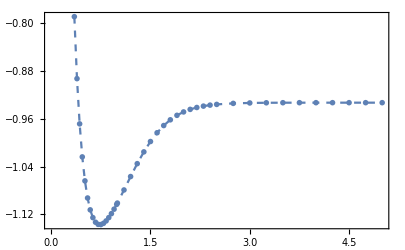

```mathematica
ListPlot[gsH2[[All,{"distance","groundstate"}]],PlotMarkers->{"OpenMarkers",6},PlotStyle->Dashed,Joined->True,Frame->True]
```

## VQE on the virtual device using random ansatz methode

All measurements are perfect here.

### (1) Original noisy setting: H2onSQC0.mx

Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H2onSQC0, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H2onSQC0.mx", H2onSQC0];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH2}]

Compilation with automatically generated ansatz at Mon 20 Feb 2023 19:53:13 with grad NGAN

@cycle1:Mon 20 Feb 2023 19:54:32, fev:577, <E>: -0.5550180898506145 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 3, 13}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 19:56:16, fev:979, <E>: -0.5550180898506145 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 3, 27}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 19:59:11, fev:1525, <E>: -0.5550180898506145 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 3, 42}

dist 0.35 ; runtime 6.07908 min ; ϵ=0.234251

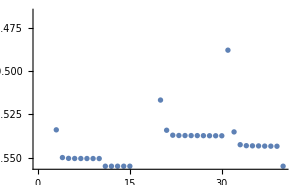

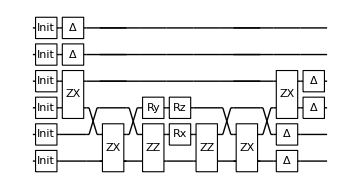

Compilation with automatically generated ansatz at Mon 20 Feb 2023 19:59:18 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:00:45, fev:566, <E>: -0.6843486235545928 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 11, 12}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:02:17, fev:1011, <E>: -0.6843486235545928 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 11, 25}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:04:38, fev:1558, <E>: -0.6843486235545928 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 11, 45}

dist 0.39 ; runtime 5.47466 min ; ϵ=0.208614

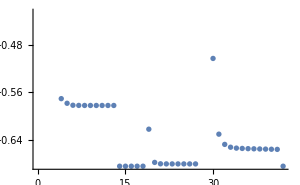

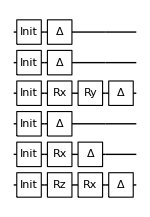

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:04:47 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:06:01, fev:400, <E>: -0.16635551014530156 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 7, 24}

@cycle2:Mon 20 Feb 2023 20:07:31, fev:857, <E>: -0.12009143542913978 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 10, 41}

@cycle3:Mon 20 Feb 2023 20:08:53, fev:1334, <E>: -0.7432220464647524 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 17, 61}

@cycle4:Mon 20 Feb 2023 20:09:43, fev:1721, <E>: -0.16635551014531155 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 15, 1, 20, 68}

@cycle5:Mon 20 Feb 2023 20:11:17, fev:2207, <E>: -0.7639666448926211 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 21, 1, 25, 85}

Slowing down @cycle 6

@cycle6:Mon 20 Feb 2023 20:12:22, fev:2568, <E>: -0.7639666448926211 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 21, 1, 25, 93}

Slowing down @cycle 7

@cycle7:Mon 20 Feb 2023 20:14:04, fev:3088, <E>: -0.7639666448926211 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 21, 1, 25, 105}

dist 0.43 ; runtime 9.49069 min ; ϵ=0.204639

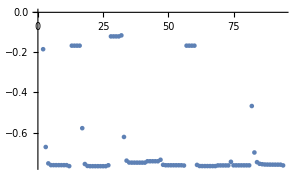

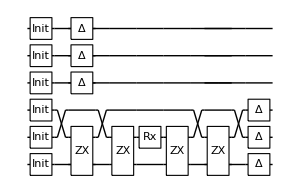

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:14:16 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:15:39, fev:517, <E>: -0.8064833105473681 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 10, 12}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:17:09, fev:928, <E>: -0.8064833105473681 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 10, 17}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:19:24, fev:1462, <E>: -0.8064833105473681 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 10, 29}

dist 0.47 ; runtime 5.15743 min ; ϵ=0.21739

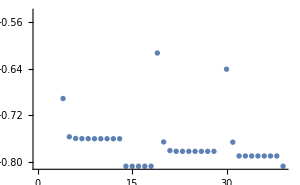

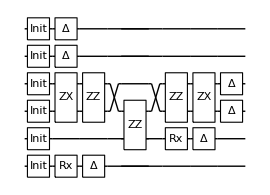

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:19:26 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:20:24, fev:414, <E>: -0.31025201130750013 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 7, 16}

@cycle2:Mon 20 Feb 2023 20:21:41, fev:879, <E>: -0.8734566727437929 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 10, 25}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:22:38, fev:1208, <E>: -0.8734566727437929 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 10, 34}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 20:24:11, fev:1663, <E>: -0.8734566727437929 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 10, 40}

dist 0.51 ; runtime 4.77469 min ; ϵ=0.190533

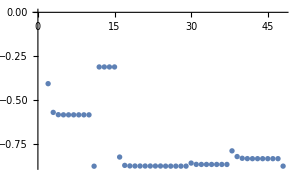

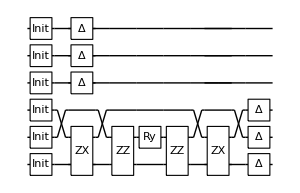

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:24:12 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:25:09, fev:412, <E>: -0.6367240191369612 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 5, 14}

@cycle2:Mon 20 Feb 2023 20:26:42, fev:948, <E>: -0.9119178802346045 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 13, 30}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:27:29, fev:1273, <E>: -0.9119178802346045 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 13, 43}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 20:28:41, fev:1718, <E>: -0.9119178802346045 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 13, 52}

dist 0.55 ; runtime 4.48524 min ; ϵ=0.180712

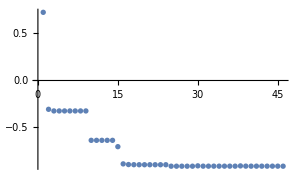

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:28:42 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:29:52, fev:440, <E>: -0.9367426022708395 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 3, 12}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:31:07, fev:815, <E>: -0.9367426022708395 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 3, 30}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:33:10, fev:1335, <E>: -0.9367426022708395 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 3, 57}

dist 0.59 ; runtime 4.4888 min ; ϵ=0.175718

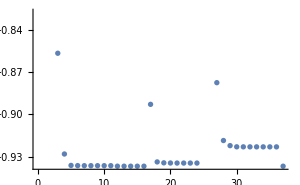

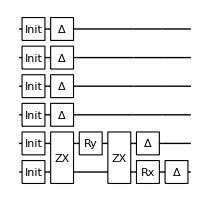

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:33:11 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:34:34, fev:543, <E>: -0.9555190585166795 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 13, 19}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:36:09, fev:993, <E>: -0.9555190585166795 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 13, 28}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:38:38, fev:1549, <E>: -0.9555190585166795 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 13, 38}

dist 0.63 ; runtime 5.51875 min ; ϵ=0.169951

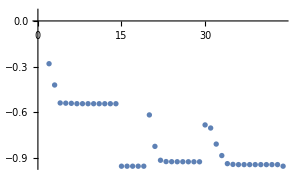

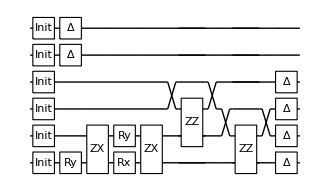

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:38:42 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:40:25, fev:627, <E>: -0.4633273449441151 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 1, 0, 0, 22}

@cycle2:Mon 20 Feb 2023 20:42:43, fev:1210, <E>: -0.4637800699128052 nansatz: 3 merged-smallθ-metric-bf-gmerged: {2, 9, 0, 11, 36}

@cycle3:Mon 20 Feb 2023 20:44:12, fev:1678, <E>: -0.9678614666572014 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 24, 0, 15, 52}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 20:45:03, fev:2041, <E>: -0.9678614666572014 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 24, 0, 15, 63}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 20:46:08, fev:2464, <E>: -0.9678614666572014 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 24, 0, 15, 81}

dist 0.67 ; runtime 7.43416 min ; ϵ=0.165313

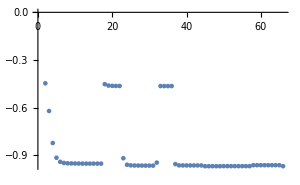

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:46:08 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:47:18, fev:515, <E>: -0.9556618597306425 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 1, 18}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:49:06, fev:985, <E>: -0.9556618597306425 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 1, 25}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:51:32, fev:1537, <E>: -0.9556618597306425 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 1, 37}

dist 0.71 ; runtime 5.46293 min ; ϵ=0.181089

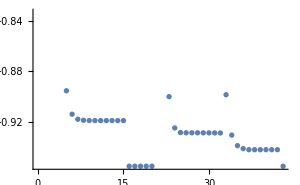

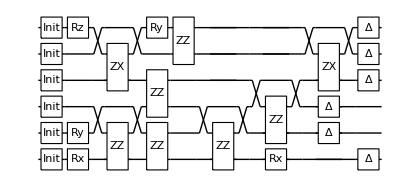

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:51:36 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:52:56, fev:501, <E>: -0.9796595478362362 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 7, 14}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 20:54:16, fev:894, <E>: -0.9796595478362362 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 7, 27}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 20:56:10, fev:1397, <E>: -0.9796595478362362 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 7, 47}

dist 0.75 ; runtime 4.56738 min ; ϵ=0.157458

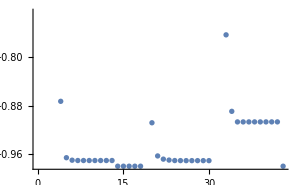

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 20:56:10 with grad NGAN

@cycle1:Mon 20 Feb 2023 20:57:18, fev:429, <E>: -0.5151393197409295 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 3, 19}

@cycle2:Mon 20 Feb 2023 20:59:06, fev:990, <E>: -0.9529098053003884 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 7, 29}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 21:00:18, fev:1339, <E>: -0.9529098053003884 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 7, 32}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 21:02:07, fev:1810, <E>: -0.9529098053003884 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 7, 36}

dist 0.79 ; runtime 6.04574 min ; ϵ=0.182087

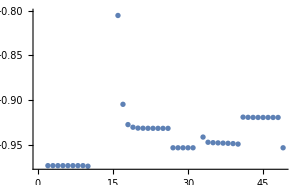

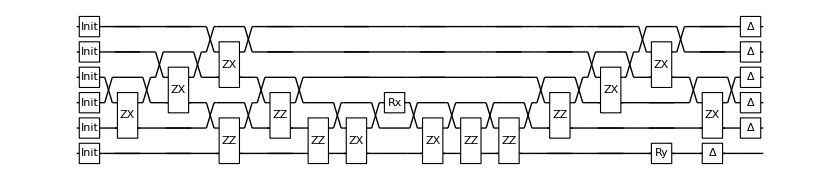

Compilation with automatically generated ansatz at Mon 20 Feb 2023 21:02:13 with grad NGAN

@cycle1:Mon 20 Feb 2023 21:03:23, fev:569, <E>: -0.978763074868003 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 9, 12}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 21:04:40, fev:974, <E>: -0.978763074868003 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 9, 20}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 21:06:43, fev:1477, <E>: -0.978763074868003 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 9, 39}

dist 0.83 ; runtime 4.51091 min ; ϵ=0.152195

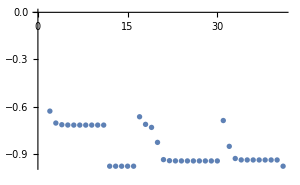

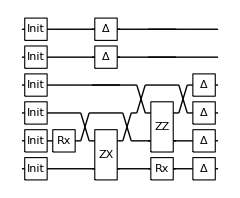

Compilation with automatically generated ansatz at Mon 20 Feb 2023 21:06:44 with grad NGAN

@cycle1:Mon 20 Feb 2023 21:07:56, fev:511, <E>: -0.7390884858640564 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 15, 8}

@cycle2:Mon 20 Feb 2023 21:09:27, fev:1047, <E>: -0.9727074639455635 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 22, 19}

@cycle3:Mon 20 Feb 2023 21:10:25, fev:1423, <E>: -0.00795991282896541 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 17, 0, 23, 28}

@cycle4:Mon 20 Feb 2023 21:17:38, fev:2087, <E>: 0.3887182069775942 nansatz: 0 merged-smallθ-metric-bf-gmerged: {1, 47, 0, 35, 74}

@cycle5:Mon 20 Feb 2023 21:47:35, fev:3902, <E>: -0.9505228681425015 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 106, 0, 104, 145}

@cycle6:Mon 20 Feb 2023 21:49:05, fev:4421, <E>: -0.9542443882144418 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 112, 0, 105, 152}

Slowing down @cycle 7

@cycle7:Mon 20 Feb 2023 21:50:23, fev:4779, <E>: -0.9542443882144418 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 112, 0, 105, 158}

Slowing down @cycle 8

@cycle8:Mon 20 Feb 2023 21:52:26, fev:5289, <E>: -0.9542443882144418 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 112, 0, 105, 169}

dist 0.87 ; runtime 45.7943 min ; ϵ=0.171201

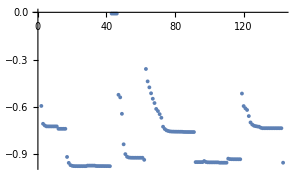

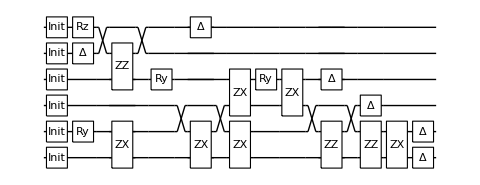

Compilation with automatically generated ansatz at Mon 20 Feb 2023 21:52:31 with grad NGAN

@cycle1:Mon 20 Feb 2023 21:53:51, fev:615, <E>: -0.5093640303915294 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 17, 11}

@cycle2:Mon 20 Feb 2023 21:55:17, fev:1138, <E>: -0.5088462088739928 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 25, 26}

@cycle3:Mon 20 Feb 2023 21:56:53, fev:1601, <E>: -0.5093639711915496 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 16, 0, 25, 40}

@cycle4:Mon 20 Feb 2023 21:58:29, fev:2115, <E>: -0.9713421680102826 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 30, 55}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 21:59:30, fev:2479, <E>: -0.9713421680102826 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 30, 63}

Slowing down @cycle 6

@cycle6:Mon 20 Feb 2023 22:00:55, fev:2946, <E>: -0.9713421680102826 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 29, 0, 30, 66}

dist 0.91 ; runtime 8.39169 min ; ϵ=0.147471

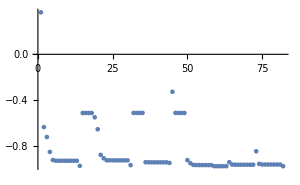

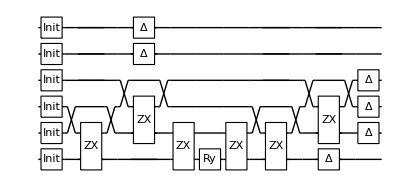

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:00:55 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:02:08, fev:557, <E>: -0.9626253162079752 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 1, 1, 3, 20}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 22:03:41, fev:983, <E>: -0.9626253162079752 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 1, 1, 3, 32}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:06:09, fev:1540, <E>: -0.9626253162079752 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 1, 1, 3, 52}

dist 0.95 ; runtime 5.28684 min ; ϵ=0.148714

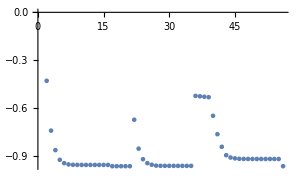

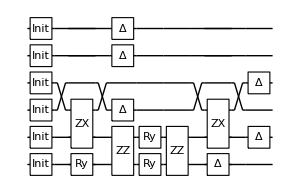

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:06:12 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:07:49, fev:563, <E>: -0.9212250260976934 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 5, 13}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 22:10:00, fev:976, <E>: -0.9212250260976934 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 5, 17}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:13:04, fev:1526, <E>: -0.9212250260976934 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 5, 24}

dist 0.99 ; runtime 7.0172 min ; ϵ=0.182023

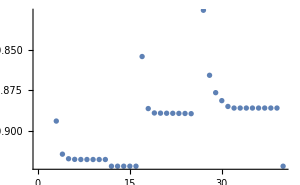

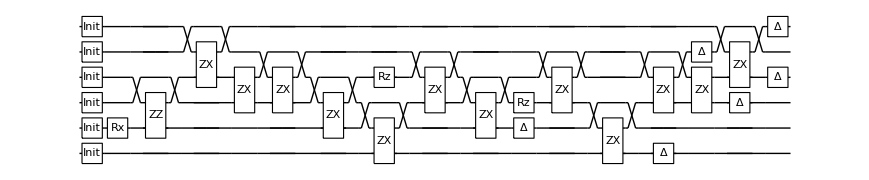

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:13:13 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:14:32, fev:579, <E>: -0.7498725070145591 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 8, 10}

@cycle2:Mon 20 Feb 2023 22:16:25, fev:1198, <E>: -0.9411967121208938 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 14, 17}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:17:38, fev:1582, <E>: -0.9411967121208938 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 14, 21}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 22:19:12, fev:2061, <E>: -0.9411967121208938 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 18, 0, 14, 27}

dist 1. ; runtime 6.04386 min ; ϵ=0.159954

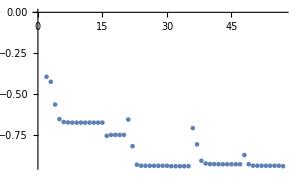

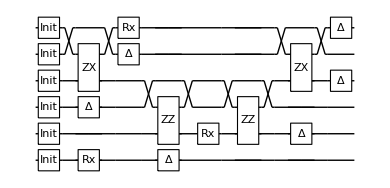

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:19:16 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:20:35, fev:478, <E>: -0.9364810935523792 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 3, 13}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 22:22:04, fev:889, <E>: -0.9364810935523792 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 3, 32}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:24:23, fev:1454, <E>: -0.9364810935523792 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 3, 45}

dist 1.1 ; runtime 5.141 min ; ϵ=0.142712

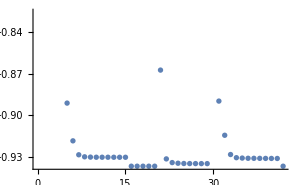

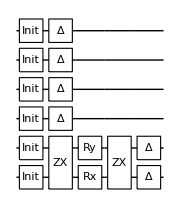

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:24:25 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:25:38, fev:496, <E>: -0.5268185364903804 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 10, 15}

@cycle2:Mon 20 Feb 2023 22:27:18, fev:1123, <E>: -0.7264167882163559 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 27}

@cycle3:Mon 20 Feb 2023 22:28:47, fev:1688, <E>: -0.9129182587851237 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 20, 1, 27, 34}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 22:29:39, fev:2040, <E>: -0.9129182587851237 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 20, 1, 27, 49}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 22:30:43, fev:2467, <E>: -0.9129182587851237 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 20, 1, 27, 59}

dist 1.2 ; runtime 6.31146 min ; ϵ=0.143822

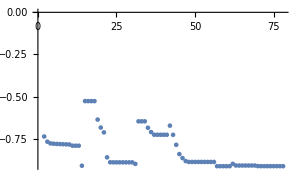

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:30:43 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:32:11, fev:594, <E>: -0.7278634328630039 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 14, 15}

@cycle2:Mon 20 Feb 2023 22:34:09, fev:1173, <E>: -0.8861834459381892 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 26, 24}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 22:35:13, fev:1512, <E>: -0.8861834459381892 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 26, 32}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 22:36:58, fev:2026, <E>: -0.8861834459381892 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 26, 44}

dist 1.3 ; runtime 6.2502 min ; ϵ=0.149003

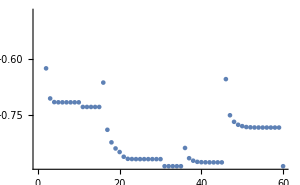

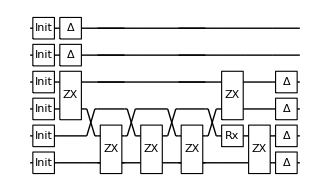

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:36:58 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:38:13, fev:469, <E>: -0.6185831585910342 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 0, 23}

@cycle2:Mon 20 Feb 2023 22:39:53, fev:1022, <E>: -0.6207005351221532 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 0, 30}

@cycle3:Mon 20 Feb 2023 22:41:50, fev:1617, <E>: -0.8623033748700631 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 18, 35}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 22:42:51, fev:1984, <E>: -0.8623033748700631 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 18, 53}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 22:44:09, fev:2419, <E>: -0.8623033748700631 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 21, 0, 18, 71}

dist 1.4 ; runtime 7.18862 min ; ϵ=0.153165

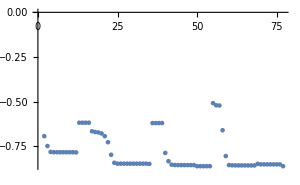

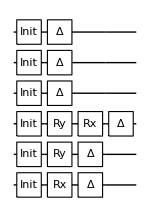

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:44:10 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:45:16, fev:388, <E>: -0.36882951306078204 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 0, 17}

@cycle2:Mon 20 Feb 2023 22:46:34, fev:842, <E>: -0.8011952283043385 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 2, 29}

@cycle3:Mon 20 Feb 2023 22:47:43, fev:1332, <E>: -0.539368828296569 nansatz: 1 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 10, 32}

@cycle4:Mon 20 Feb 2023 22:48:43, fev:1726, <E>: -0.835932453505701 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 11, 43}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 22:49:35, fev:2025, <E>: -0.835932453505701 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 11, 50}

Slowing down @cycle 6

@cycle6:Mon 20 Feb 2023 22:50:51, fev:2448, <E>: -0.835932453505701 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 11, 59}

dist 1.5 ; runtime 6.68806 min ; ϵ=0.162217

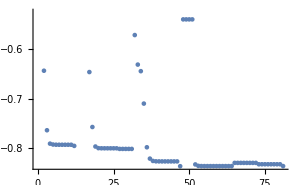

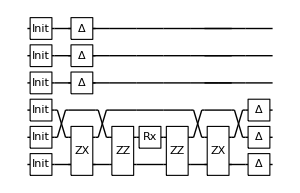

Compilation with automatically generated ansatz at Mon 20 Feb 2023 22:50:51 with grad NGAN

@cycle1:Mon 20 Feb 2023 22:52:15, fev:575, <E>: -0.6311532258540559 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 12, 13}

@cycle2:Mon 20 Feb 2023 22:54:07, fev:1141, <E>: 0.15134300079150909 nansatz: 1 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 29, 20}

@cycle3:Mon 20 Feb 2023 23:04:26, fev:2028, <E>: -0.8139319336185973 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 74, 64}

Slowing down @cycle 4

@cycle4:Mon 20 Feb 2023 23:05:27, fev:2410, <E>: -0.8139319336185973 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 74, 78}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 23:06:45, fev:2866, <E>: -0.8139319336185973 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 52, 0, 74, 97}

dist 1.6 ; runtime 15.895 min ; ϵ=0.169541

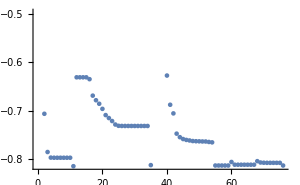

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:06:45 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:08:14, fev:562, <E>: -0.46552314202335976 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 0, 22}

@cycle2:Mon 20 Feb 2023 23:10:08, fev:1211, <E>: -0.5003930292818667 nansatz: 1 merged-smallθ-metric-bf-gmerged: {2, 16, 0, 11, 43}

@cycle3:Mon 20 Feb 2023 23:11:26, fev:1787, <E>: -0.6642764604058459 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 22, 0, 14, 57}

@cycle4:Mon 20 Feb 2023 23:12:59, fev:2337, <E>: -0.8266334873320005 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 25, 65}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 23:13:56, fev:2677, <E>: -0.8266334873320005 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 34, 0, 25, 72}

@cycle6:Mon 20 Feb 2023 23:15:26, fev:3203, <E>: -0.8279169564764032 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 37, 0, 25, 85}

Slowing down @cycle 7

@cycle7:Mon 20 Feb 2023 23:16:45, fev:3649, <E>: -0.8279169564764032 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 37, 0, 25, 95}

Slowing down @cycle 8

@cycle8:Mon 20 Feb 2023 23:18:36, fev:4215, <E>: -0.8279169564764032 nansatz: 4 merged-smallθ-metric-bf-gmerged: {2, 37, 0, 25, 109}

dist 1.7 ; runtime 11.8564 min ; ϵ=0.14351

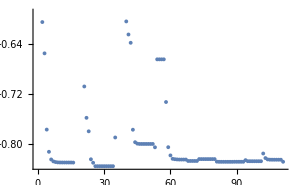

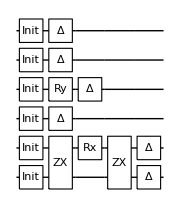

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:18:36 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:19:41, fev:397, <E>: -0.835859642681453 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 0, 19}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 23:20:49, fev:752, <E>: -0.835859642681453 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 0, 33}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:22:37, fev:1210, <E>: -0.835859642681453 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 0, 44}

dist 1.8 ; runtime 4.00976 min ; ϵ=0.125957

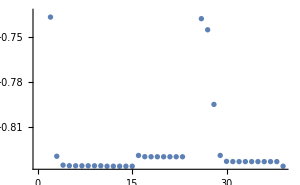

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:22:37 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:23:59, fev:502, <E>: -0.8332668489343609 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 7, 8}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 23:25:46, fev:941, <E>: -0.8332668489343609 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 7, 18}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:28:16, fev:1489, <E>: -0.8332668489343609 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 7, 31}

dist 1.9 ; runtime 5.67542 min ; ϵ=0.120174

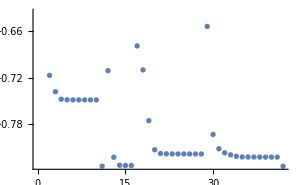

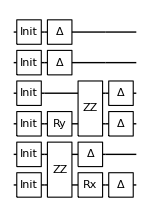

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:28:18 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:29:41, fev:517, <E>: -0.8155386177022258 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 2, 14}

@cycle2:Mon 20 Feb 2023 23:32:02, fev:1176, <E>: -0.8359784683038298 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 6, 25}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:33:17, fev:1527, <E>: -0.8359784683038298 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 6, 29}

@cycle4:Mon 20 Feb 2023 23:35:53, fev:2319, <E>: -0.8375007795515776 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 12, 38}

Slowing down @cycle 5

@cycle5:Mon 20 Feb 2023 23:38:25, fev:2830, <E>: -0.8375007795515776 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 12, 50}

Slowing down @cycle 6

@cycle6:Mon 20 Feb 2023 23:42:00, fev:3491, <E>: -0.8375007795515776 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 26, 0, 12, 61}

dist 2. ; runtime 13.8016 min ; ϵ=0.11114

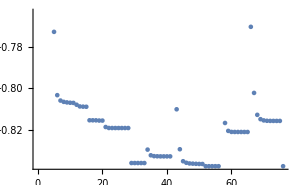

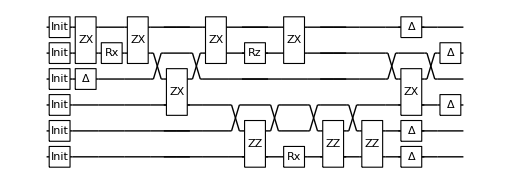

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:42:06 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:43:22, fev:505, <E>: -0.8502220515806023 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 7, 22}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 23:44:45, fev:883, <E>: -0.8502220515806023 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 7, 35}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:46:57, fev:1415, <E>: -0.8502220515806023 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 7, 52}

dist 2.1 ; runtime 4.92704 min ; ϵ=0.0941526

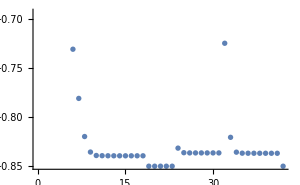

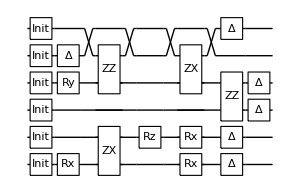

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:47:02 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:47:55, fev:389, <E>: -0.8482059580135987 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 0, 28}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 23:49:08, fev:762, <E>: -0.8482059580135987 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 0, 40}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:50:56, fev:1248, <E>: -0.8482059580135987 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 0, 56}

dist 2.2 ; runtime 3.90727 min ; ϵ=0.0930181

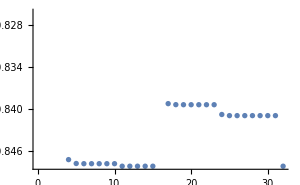

-Graphics-

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:50:56 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:52:04, fev:448, <E>: -0.8392958867613508 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 9, 15}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 23:53:22, fev:810, <E>: -0.8392958867613508 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 9, 19}

Slowing down @cycle 3

@cycle3:Mon 20 Feb 2023 23:55:42, fev:1324, <E>: -0.8392958867613508 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 9, 35}

dist 2.3 ; runtime 4.80719 min ; ϵ=0.0950332

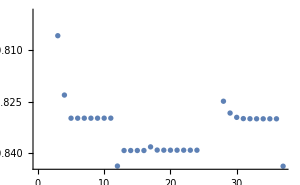

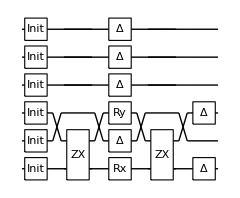

Compilation with automatically generated ansatz at Mon 20 Feb 2023 23:55:45 with grad NGAN

@cycle1:Mon 20 Feb 2023 23:56:56, fev:446, <E>: -0.8500412091062634 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 7}

Slowing down @cycle 2

@cycle2:Mon 20 Feb 2023 23:58:25, fev:820, <E>: -0.8500412091062634 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 24}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 00:00:41, fev:1325, <E>: -0.8500412091062634 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 5, 42}

dist 2.4 ; runtime 4.98463 min ; ϵ=0.0872137

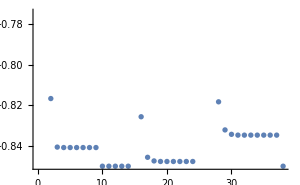

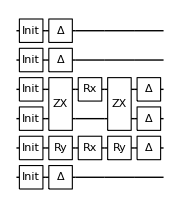

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:00:44 with grad NGAN

@cycle1:Tue 21 Feb 2023 00:01:59, fev:559, <E>: -0.8499451795864797 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 9, 13}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 00:03:25, fev:936, <E>: -0.8499451795864797 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 9, 20}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 00:05:54, fev:1452, <E>: -0.8499451795864797 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 9, 30}

dist 2.5 ; runtime 5.21558 min ; ϵ=0.0861097

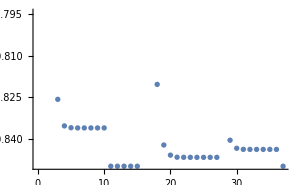

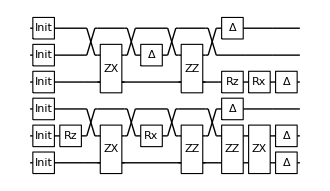

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:05:57 with grad NGAN

@cycle1:Tue 21 Feb 2023 00:07:12, fev:522, <E>: -0.8448056942664557 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 5, 17}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 00:08:50, fev:921, <E>: -0.8448056942664557 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 5, 35}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 00:11:14, fev:1453, <E>: -0.8448056942664557 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 5, 52}

dist 2.75 ; runtime 5.35705 min ; ϵ=0.0895433

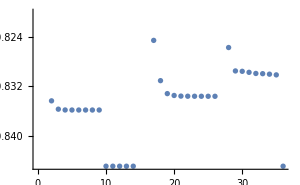

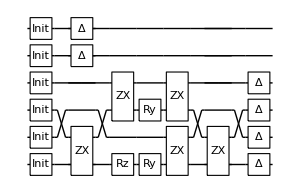

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:11:18 with grad NGAN

@cycle1:Tue 21 Feb 2023 00:12:19, fev:402, <E>: -0.8518915627523329 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 24}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 00:13:34, fev:776, <E>: -0.8518915627523329 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 30}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 00:15:22, fev:1262, <E>: -0.8518915627523329 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 0, 52}

dist 3. ; runtime 4.06931 min ; ϵ=0.0817403

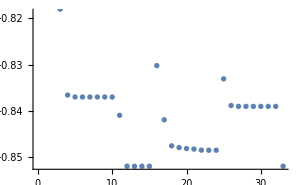

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:15:22 with grad NGAN

@cycle1:Tue 21 Feb 2023 00:16:19, fev:421, <E>: 0.0061488021510006236 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 3, 23}

@cycle2:Tue 21 Feb 2023 00:17:43, fev:919, <E>: -0.6033577603007498 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 3, 35}

@cycle3:Tue 21 Feb 2023 00:19:02, fev:1430, <E>: -0.8220493001681303 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 24, 0, 13, 35}

Slowing down @cycle 4

@cycle4:Tue 21 Feb 2023 00:20:06, fev:1773, <E>: -0.8220493001681303 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 24, 0, 13, 41}

@cycle5:Tue 21 Feb 2023 00:21:54, fev:2419, <E>: -0.830567074549527 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 30, 0, 15, 47}

@cycle6:Tue 21 Feb 2023 00:25:09, fev:3314, <E>: -0.8370208182497888 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 21, 52}

Slowing down @cycle 7

@cycle7:Tue 21 Feb 2023 00:27:48, fev:3846, <E>: -0.8370208182497888 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 21, 59}

@cycle8:Tue 21 Feb 2023 00:32:16, fev:4819, <E>: -0.8371734167812426 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 47, 0, 27, 69}

@cycle9:Tue 21 Feb 2023 00:36:43, fev:5769, <E>: -0.854693096501105 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 56, 0, 41, 79}

Slowing down @cycle 10

@cycle10:Tue 21 Feb 2023 00:39:57, fev:6423, <E>: -0.854693096501105 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 56, 0, 41, 88}

@cycle11:Tue 21 Feb 2023 00:44:04, fev:7425, <E>: -0.8558652335100916 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 44, 96}

Slowing down @cycle 12

@cycle12:Tue 21 Feb 2023 00:48:17, fev:8211, <E>: -0.8558652335100916 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 44, 108}

Slowing down @cycle 13

@cycle13:Tue 21 Feb 2023 00:53:53, fev:9145, <E>: -0.8558652335100916 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 65, 0, 44, 119}

dist 3.25 ; runtime 39.0984 min ; ϵ=0.077476

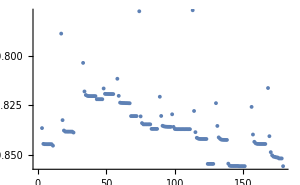

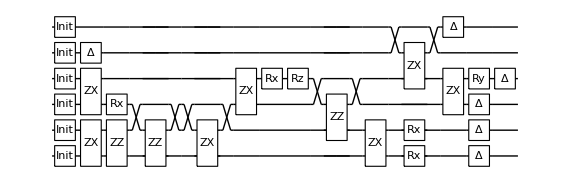

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:54:28 with grad NGAN

@cycle1:Tue 21 Feb 2023 00:55:38, fev:467, <E>: -0.849960522230513 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 6, 12}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 00:56:59, fev:800, <E>: -0.849960522230513 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 6, 19}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 00:59:23, fev:1327, <E>: -0.849960522230513 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 6, 35}

dist 3.5 ; runtime 4.97013 min ; ϵ=0.0832679

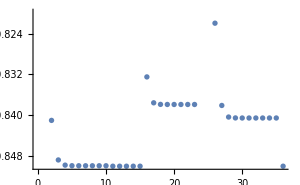

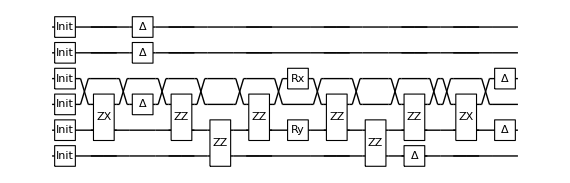

Compilation with automatically generated ansatz at Tue 21 Feb 2023 00:59:27 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:00:39, fev:549, <E>: -0.8472849358658603 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 6, 19}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 01:02:12, fev:956, <E>: -0.8472849358658603 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 6, 29}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:04:14, fev:1453, <E>: -0.8472849358658603 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 6, 49}

dist 3.75 ; runtime 4.79774 min ; ϵ=0.0859015

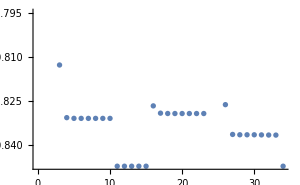

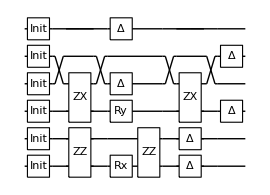

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:04:15 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:05:26, fev:481, <E>: -0.8409228220854252 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 5}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 01:06:54, fev:855, <E>: -0.8409228220854252 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 10}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:09:25, fev:1367, <E>: -0.8409228220854252 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 4, 22}

dist 4. ; runtime 5.1771 min ; ϵ=0.0922485

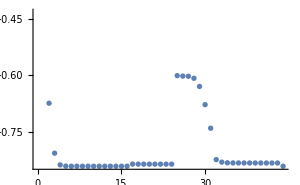

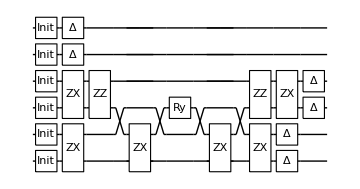

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:09:25 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:10:41, fev:540, <E>: -0.8514098811012203 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 12, 7}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 01:12:06, fev:931, <E>: -0.8514098811012203 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 12, 25}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:14:26, fev:1443, <E>: -0.8514098811012203 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 12, 48}

dist 4.25 ; runtime 5.05319 min ; ϵ=0.0817563

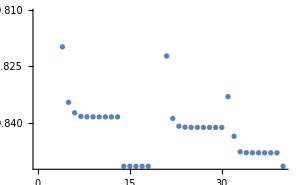

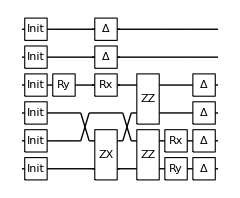

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:14:29 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:15:37, fev:505, <E>: -0.8364647971944967 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 15}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 01:16:55, fev:885, <E>: -0.8364647971944967 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 24}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:18:56, fev:1396, <E>: -0.8364647971944967 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 16, 45}

dist 4.5 ; runtime 4.46333 min ; ϵ=0.0966997

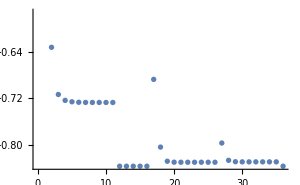

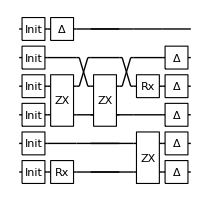

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:18:56 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:20:04, fev:404, <E>: -0.8516980858397782 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 1, 17}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 01:21:11, fev:761, <E>: -0.8516980858397782 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 1, 32}

Slowing down @cycle 3

@cycle3:Tue 21 Feb 2023 01:23:00, fev:1237, <E>: -0.8516980858397782 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 1, 55}

dist 4.75 ; runtime 4.06235 min ; ϵ=0.0814658

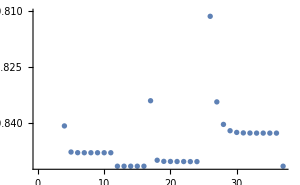

-Graphics-

Compilation with automatically generated ansatz at Tue 21 Feb 2023 01:23:00 with grad NGAN

@cycle1:Tue 21 Feb 2023 01:24:09, fev:491, <E>: -0.8299702583714819 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 3, 19}

Slowing down @cycle 2

@cycle2:Tue 21 Feb 2023 01:25:36, fev:853, <E>: -0.8299702583714819 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 3, 26}

@cycle3:Tue 21 Feb 2023 01:28:20, fev:1531, <E>: -0.4447228589318093 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 19, 39}

@cycle4:Tue 21 Feb 2023 03:11:35, fev:3380, <E>: -0.6516400971120351 nansatz: 65 merged-smallθ-metric-bf-gmerged: {1, 139, 0, 93, 192}

@cycle5:Tue 21 Feb 2023 03:32:26, fev:4976, <E>: -0.7768312942239343 nansatz: 61 merged-smallθ-metric-bf-gmerged: {1, 178, 0, 134, 208}

Slowing down @cycle 6

@cycle6:Tue 21 Feb 2023 03:39:08, fev:5545, <E>: -0.7768312942239343 nansatz: 61 merged-smallθ-metric-bf-gmerged: {1, 178, 0, 134, 231}

@cycle7:Tue 21 Feb 2023 03:54:58, fev:7547, <E>: -0.8197386533044071 nansatz: 34 merged-smallθ-metric-bf-gmerged: {1, 191, 0, 183, 253}

Slowing down @cycle 8

@cycle8:Tue 21 Feb 2023 04:00:49, fev:8181, <E>: -0.8197386533044071 nansatz: 34 merged-smallθ-metric-bf-gmerged: {1, 191, 0, 183, 260}

@cycle9:Tue 21 Feb 2023 04:11:47, fev:9506, <E>: -0.7912453029704166 nansatz: 46 merged-smallθ-metric-bf-gmerged: {1, 201, 0, 193, 270}

Slowing down @cycle 10

@cycle10:Tue 21 Feb 2023 04:24:02, fev:10363, <E>: -0.7912453029704166 nansatz: 46 merged-smallθ-metric-bf-gmerged: {1, 201, 0, 193, 292}

Slowing down @cycle 11

@cycle11:Tue 21 Feb 2023 04:40:24, fev:11405, <E>: -0.7912453029704166 nansatz: 46 merged-smallθ-metric-bf-gmerged: {1, 201, 0, 193, 317}

dist 5. ; runtime 198.718 min ; ϵ=0.120947

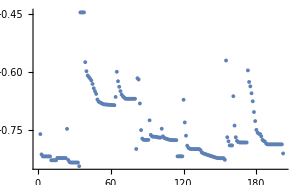

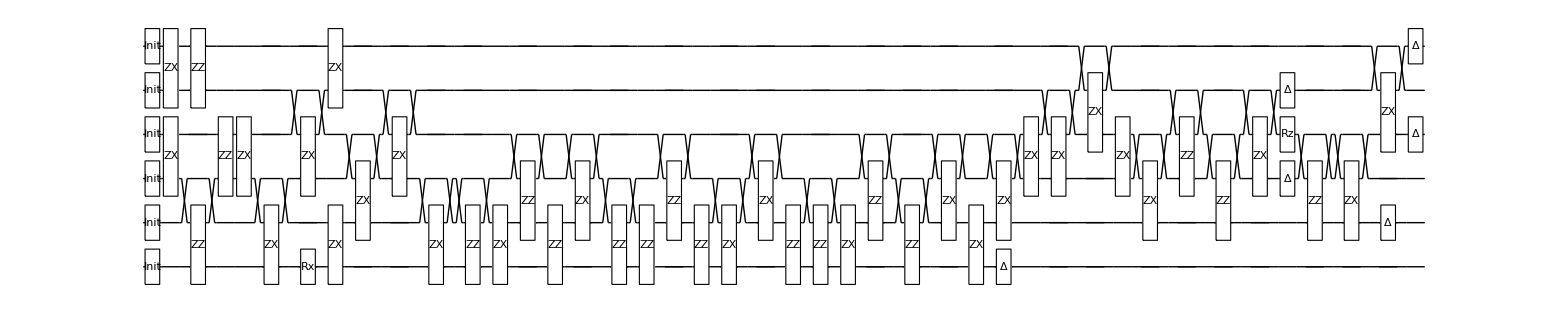

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### (1) Original noisy setting: H2onSQC1.mx

```mathematica
H2onSQC1={};
```

Table[
 {distance, hamfile, hamiltonian, groundstate} = Values@data;
 dev = SuperconductingHub[];
 conf = DefaultConfig[dev, hamiltonian];
 conf["groundstate"] = groundstate;
    res = VQEonVQD[conf];
 {runtime, cost, Elist, ansatz, θvars, finmsg, ncycle, fev, aborted, cycleres, elimmerge, elimbfsmall, elimmetov, elimbf} = res;
 AppendTo[H2onSQC0, <|"runtime" -> runtime, "ansatz" -> ansatz, "θvars" -> θvars, "groundstate" -> groundstate, "cost" -> cost, "fev" -> fev|>];
 DumpSave["H2onSQC0.mx", H2onSQC0];
 Print["dist ", distance, " ; runtime ", runtime, " ; ϵ=", Last@Elist - conf["groundstate"]];
 Print[ListPlot[Elist, ImageSize -> 300]];
 Print[DrawCircuit[ansatz, 6]];
 , {data, gsH2}]